```mathematica
(* Example Code for using Mulchrone et al Strain Analysis Package *)
```

```mathematica
(* Load the package with the code in *)
```

```mathematica
<<"C:\\Users\\Dave\\Desktop\\Strain Analysis Notebook.m"
```

```mathematica
(*Specify Directory where image files are located *)
```

```mathematica
SetDirectory["C:\\Users\\Dave\\Desktop"]
```

C:\Users\Dave\Desktop

```mathematica
(* Check raw image file *)
```

```mathematica
Import["Oolite Ramsay and Huber 1983.bmp"]
```

-Graphics-

```mathematica
(* Do the image analysis *)
```

```mathematica
res1=AnalyzeImage["Oolite Ramsay and Huber 1983.bmp"]
```

-Graphics-

{{2→{52.0494,{1619.48,1655.69},148.392,73.5907,2.69583,2},«218»,221→{45.0893,{951.583,128.939},124.928,«17»,2.87361,221}},{«1»}}

```mathematica
(* Remove spurious objects by entering the object label in to the list below *)
```

```mathematica
res2=RefineImageData[res1,{51,73,121,62,49,58,95,88,82,69,154,56,80,174,211,170,28,200,210}];
```

-Graphics-

```mathematica
mres=ExtractData[res2];
(* Output from ExtractDataFromImage (mres in this case) is used for the rest of the analysis *)
```

```mathematica
(* note mres[[1]] holds the data in the form {avradius,x,y} for input to Nearest Neighbour Analysis *)
```

```mathematica
(* note mres[[2]] holds the data in the form {a,b,phi} for input to MRL Analysis *)
```

```mathematica
(* Do a nearest neighbour analysis using Mulchrone (2013) returns long axis, short axis and orientation in degrees *)
(* Axial Ratio *)
```

```mathematica
nnres=AnalyseDataPolar[mres[[1]],100]
nnres[[1]]/nnres[[2]]
```

{1.31508,0.810955,158.676}

1.62165

```mathematica
(* Create a graphical display *)
```

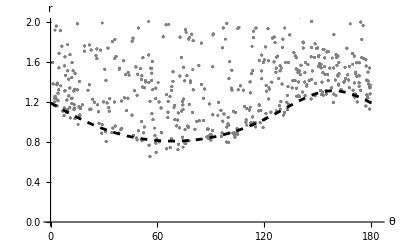

```mathematica
CreateNNPlotPolar[mres[[1]],nnres]
```

```mathematica
(* create a more typical graphical display *)
```

```mathematica
CreateNNPlotCartesian[mres[[1]],nnres]
```

-Graphics-

```mathematica
(* Perform a bootstrap analysis *)
```

```mathematica
(* Quiet prevents unecessary feedback, note this takes some time to complete! *)
```

```mathematica
bsres=Quiet[BootStrapPolar[mres[[1]],1000,200]];
```

```mathematica
(* Plot the bootstrap results with confidence intervals at 90, 95 and 99% *)
```

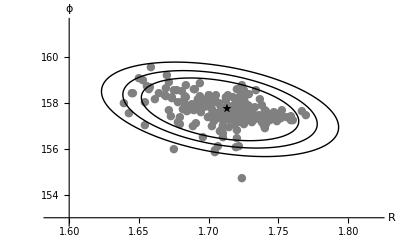

```mathematica
CreateBootStrapPlot[bsres]
```

```mathematica
(* Do strain analysis using Mean Radial Length (MRL) Mulchrone et al (2003) *)
```

```mathematica
(* Single Analysis returns axial ratio and long axis orientation *)
```

```mathematica
MRL[mres[[2]]]
```

{1.75551,-22.1505}

```mathematica
(* Bootstrap analysis *)
```

```mathematica
bsMRL=BootStrapMRL[mres[[2]],1000];
```

```mathematica
(* Plot Bootstrap results *)
```

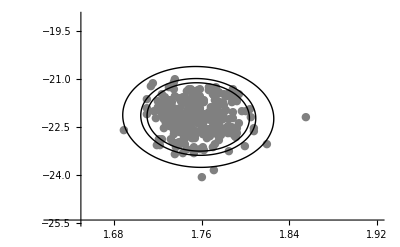

```mathematica
CreateBootStrapPlot[bsMRL]
```